```mathematica
Задача 4.
```

```mathematica
f4[x_]:=x^2 Cos[x]+1;
extrmas4=Reduce[f4'[x]==0&&x≥ (-3π)/2&&x≤ 3π,x, Reals] //N
```

x==0.||x==-3.6436||x==-1.07687||x==1.07687||x==3.6436||x==6.57833

```mathematica
mx4=NMaximize[{f4[x], (-3π)/2≤ x≤ 3π}, x]
```

{42.4032,{x→6.57833}}

```mathematica
mn4=NMinimize[{f4[x], (-3π)/2≤ x≤ 3π}, x]
```

{-87.8264,{x→9.42478}}

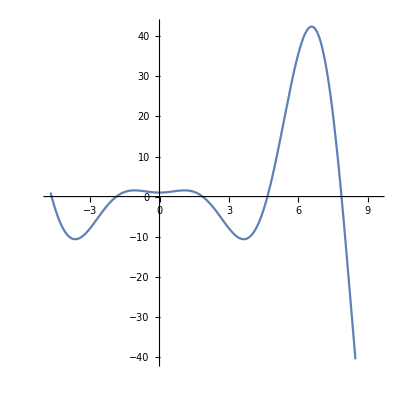

```mathematica
p4 = Plot[{f4[x]},{x,(-3π)/2, 3π}, AxesOrigin->{0,0}, AspectRatio->1]
```

```mathematica
Задание 5.
```

```mathematica
f5=-40-2x+27 x^2-10 x^3+x^4;
roots5=Reduce[f5== 0, x]
```

x==-1||x==2||x==4||x==5

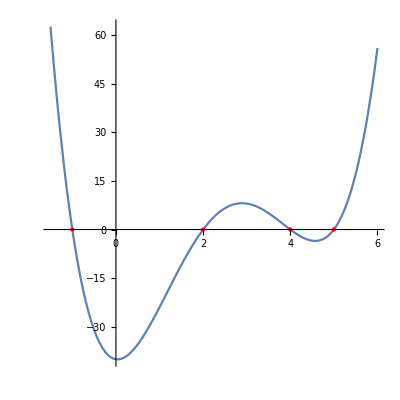

```mathematica
Plot[f5,{x, -1.5, 6}, AspectRatio->1,Mesh->{{0}}, MeshStyle->{Red,PointSize[Large]},MeshFunctions->{f5/.x-> #&}]
```

```mathematica
Задание 6.
```

```mathematica
f6[xx_, x1_,y1_, x2_, y2_, x3_, y3_]:=Module[{},koefs=Reduce[x1^2*a+x1*b+c== y1&&x2^2 a+x2*b+c== y2&&x3^2*a+x3*b+c==y3, {a,b,c}]; 
polinom=koefs[[1]][[2]]*x^2+koefs[[2]][[2]]*x+koefs[[3]][[2]]/.x->xx;polinom]
```

```mathematica
f6[x, 1, 2, 2, 2, -1, 3]
```

7/3-x/2+x^2/6

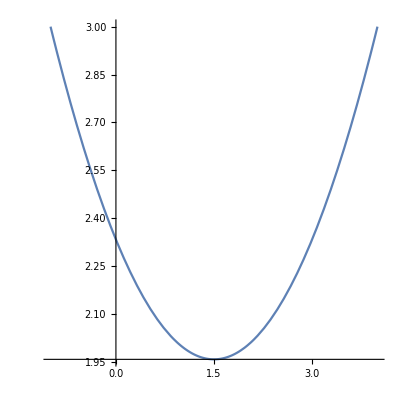

```mathematica
Plot[f6[x, 1, 2, 2, 2, -1, 3], {x,-1, 4}, AspectRatio->1]
```

```mathematica
Задания 7-9.
```

```mathematica
bisec[f_,xb_, xe_,ϵ_ ]:=Module[{x0 = xb, x00 =xe, ep=10^-ϵ, xl},
While[Abs[f[x00]-f[x0]]>ep,
xl=(x00+x0)/2;
If[f[x0]*f[xl]<0, x00=xl, x0=xl]];
N[x0, ϵ]
];
```

```mathematica
newton[f_,xb_,ϵ_ ]:=Module[{ x0=xb, ep=10^-ϵ},
While[Abs[f[x0]]>ep,
x0=x0-f[x0]/f'[x0];
];
N[x0,ϵ]
];
```

```mathematica
f9[x_]:= x^3+x^2-2x+1-Sin[x];
```

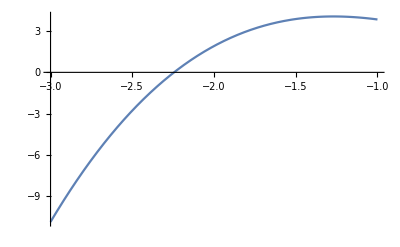

```mathematica
Plot[f9[x],{x, -3,-1}]
```

```mathematica
FindRoot[f9[x], {x, -2}]
```

{x→-2.24461}

```mathematica
bisec[f9, -3, -2, 5]
```

-2.2446

```mathematica
newton[f9, -2, 5]
```

-2.2446